### Hamiltonian Matrices

```mathematica
ClearAll[H0,t,x,y,r0,Bz,B,MeanFieldHamiltonian,Ox,Oy,q,U]
IsingModelOffset=({{0, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 1}});
H0=({{0, -1, 0, -1}, {-1, 0, -1, 0}, {0, -1, 0, -1}, {-1, 0, -1, 0}});
x=({{1, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, -1, 0}, {0, 0, 0, 0}});
y=({{0, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, -1}});
HB=({{0, 2I, 0, -2I}, {-2I, 0, 2I, 0}, {0, -2I, 0, 2I}, {2I, 0, -2I, 0}});

ml0basisvec={1,1,1,1};
ml1basisvec={1,I,-1,-I};
mln1basisvec={1,-I,-1,I};
ml0pbasisvec={1,-1,1,-1};
```

### Dynamics Operator Matrices

```mathematica
Λx12=({{0, 1, 0, 0}, {1, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});Λx13=({{0, 0, 1, 0}, {0, 0, 0, 0}, {1, 0, 0, 0}, {0, 0, 0, 0}}); Λx14=({{0, 0, 0, 1}, {0, 0, 0, 0}, {0, 0, 0, 0}, {1, 0, 0, 0}}); Λx23=({{0, 0, 0, 0}, {0, 0, 1, 0}, {0, 1, 0, 0}, {0, 0, 0, 0}}); Λx24=({{0, 0, 0, 0}, {0, 0, 0, 1}, {0, 0, 0, 0}, {0, 1, 0, 0}}); Λx34=({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 1}, {0, 0, 1, 0}});
Λy12=({{0, I, 0, 0}, {-I, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}}); Λy13=({{0, 0, I, 0}, {0, 0, 0, 0}, {-I, 0, 0, 0}, {0, 0, 0, 0}}); Λy14=({{0, 0, 0, I}, {0, 0, 0, 0}, {0, 0, 0, 0}, {-I, 0, 0, 0}}); Λy23=({{0, 0, 0, 0}, {0, 0, I, 0}, {0, -I, 0, 0}, {0, 0, 0, 0}}); Λy24=({{0, 0, 0, 0}, {0, 0, 0, I}, {0, 0, 0, 0}, {0, -I, 0, 0}}); Λy34=({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, I}, {0, 0, -I, 0}});
Λz1=({{1, 0, 0, 0}, {0, -1, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});Λz2=1/(√3)({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, -2, 0}, {0, 0, 0, 0}});Λz3=1/(√6)({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, -3}});
matrices={Λx12,Λx13,Λx14,Λx23,Λx24,Λx34,Λy12,Λy13,Λy14,Λy23,Λy24,Λy34,Λz1,Λz2,Λz3};
coefs={λx12,λx13,λx14,λx23,λx24,λx34,λy12,λy13,λy14,λy23,λy24,λy34,λz1,λz2,λz3};
Operator=Sum[coefs[[i]]*matrices[[i]],{i,1,15}];
```

### Commutators

```mathematica
H0Comm=H0.Operator-Operator.H0;
xComm=x.Operator-Operator.x;
yComm=y.Operator-Operator.y;
HBComm=HB.Operator-Operator.HB;
IsingComm=IsingModelOffset.Operator-Operator.IsingModelOffset;
```

### Thermodynamic Functions

```mathematica
MeanFieldHamiltonian[J_,B_,Ox_,Oy_,J2_]:=H0-4*J*(Ox*x+Oy*y)+2J*(Ox^2+Oy^2)*IdentityMatrix[4]+B*HB+IsingModelOffset*J2;
Z[β_,J_,B_,Ox_,Oy_,J2_]:=Tr[MatrixExp[-β*MeanFieldHamiltonian[J,B,Ox,Oy,J2]]];
F[β_,J_,B_,Ox_,Oy_,J2_]:=-1/β Log[Z[β,J,B,Ox,Oy,J2]]
```

### Dynamical Equation

```mathematica
(*Expx, Expy are <x>, <y>. ExpxComm, ExpyComm are <[x,O]>, <[y,O]}*)
DynamicsEquation[Q_,J_,B_,Expx_,Expy_,J2_,ExpxComm_,ExpyComm_]:=H0Comm+J2*IsingComm+B*HBComm-J*(4*(Expx*xComm+Expy*yComm)+Q*(ExpxComm *x+ExpyComm*y))
```

## Dynamics Solver

```mathematica
(*Parameters*)
T0=.1;
qx=0; qy=0;
Q0=2*Cos[qx]+2*Cos[qy];
J0=.3;
J2=0;
freqArr={};
OArr={};
ExpxArr={};
ExpyArr={};
energies = {};
coefArr={};
probs={};
transitionElems={};
Bmin=0.01;Bmax=1;dB=.05;
(*Loop over magnetic field*)
Monitor[For[B=Bmin,B<=Bmax,B+=dB,
	(*Minimize the Free Energy with respect to the order parameters*)
	{Ox,Oy}={a,b}/.FindMinimum[{F[1/T0,J0,B,a,b,J2],a^2+b^2<=25},{{a,.1},{b,0}}][[2]];
	AppendTo[OArr,{B, Ox,Oy}];
	
	(*Solve Mean Field Theory Hamiltonian*)
	{{E1,E2,E3,E4},{ψ1,ψ2,ψ3,ψ4}}=Eigensystem[MeanFieldHamiltonian[J0,B,Ox,Oy,J2]];
	z=Exp[-E1/T0]+Exp[-E2/T0]+Exp[-E3/T0]+Exp[-E4/T0];
	p1=Exp[-E1/T0]/z;p2=Exp[-E2/T0]/z;p3=Exp[-E3/T0]/z;p4=Exp[-E4/T0]/z;
	(*Calculate Position Expectation Values *)
	Expx=p1*(ConjugateTranspose[ψ1].x.ψ1)+p2*(ConjugateTranspose[ψ2].x.ψ2)+p3*(ConjugateTranspose[ψ3].x.ψ3)+p4*(ConjugateTranspose[ψ4].x.ψ4);
	Expy=p1*(ConjugateTranspose[ψ1].y.ψ1)+p2*(ConjugateTranspose[ψ2].y.ψ2)+p3*(ConjugateTranspose[ψ3].y.ψ3)+p4*(ConjugateTranspose[ψ4].y.ψ4);
	(*Calculate Commutator Expectation Values*)
	ExpxComm=p1*(ConjugateTranspose[ψ1].xComm.ψ1)+p2*(ConjugateTranspose[ψ2].xComm.ψ2)+p3*(ConjugateTranspose[ψ3].xComm.ψ3)+p4*(ConjugateTranspose[ψ4].xComm.ψ4);
	ExpyComm=p1*(ConjugateTranspose[ψ1].yComm.ψ1)+p2*(ConjugateTranspose[ψ2].yComm.ψ2)+p3*(ConjugateTranspose[ψ3].yComm.ψ3)+p4*(ConjugateTranspose[ψ4].yComm.ψ4);
	(*Calculate Coefficients Array *)
	EquationCoefficients=ConstantArray[ 0,{15,15}];
	For[i=1,i<=15,i++,
	For[j=1, j<=15,j++,
	EquationCoefficients[[i,j]]=.5*(Tr[DynamicsEquation[Q0,J0,B,Expx,Expy,J2,ExpxComm,ExpyComm].matrices[[i]]]/.{Table[If[k!=j,coefs[[k]]->0,coefs[[k]]->1],{k,1,15}]})[[1]];
	]
	];
	(* Get Frequncies*)                 
	freqs=Re[Eigenvalues[EquationCoefficients]];
	coefVecs=Eigenvectors[EquationCoefficients];
	For[l=1,l<=Length[coefVecs],l++,
		(* Evaluate Operator Transition Elements *)
		op=Sum[coefVecs[[l]][[p]]*matrices[[p]],{p,1,15}];
		Op01=ConjugateTranspose[ml0basisvec].op.ml1basisvec;
		Op0n1=ConjugateTranspose[ml0basisvec].op.mln1basisvec;
		Op00p=ConjugateTranspose[ml0basisvec].op.ml0pbasisvec;
		Op1n1=ConjugateTranspose[mln1basisvec].op.ml1basisvec;
		Op10p=ConjugateTranspose[ml0pbasisvec].op.ml1basisvec;
		Opn10p=ConjugateTranspose[ml0pbasisvec].op.mln1basisvec;
		AppendTo[transitionElems,{B,freqs[[l]],Op01,Op0n1,Op00p,Op1n1,Op10p,Opn10p}];
	];
	AppendTo[freqArr,Join[{B},Sort[freqs]]];
], {B, Ox, Oy}]
```

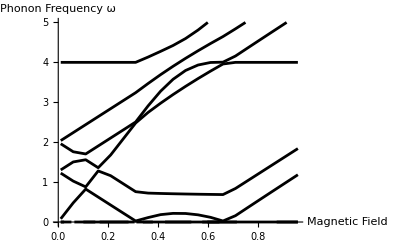

```mathematica
p1=ListLinePlot[Table[freqArr[[;;,{1,i}]],{i,2,16}],PlotStyle->{{Black,PointSize[Small]}},AxesLabel->{"Magnetic Field", "Phonon Frequency ω"},PlotRange->{0,5}];
p2=ListLinePlot[OArr[[;;,{1,2}]],PlotStyle->Blue AxesLabel->{"Magnetic Field","Order Parameter <x>"}];
Show[p1]
```